Exercises for Section 35 | Natural Language Understanding

Use Interpreter to find the location of the Eiffel Tower. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

Use Interpreter to find a university referred to as “U of T”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

Use Interpreter to find the chemicals referred to as C2H4, C2H6 and C3H8. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

Use Interpreter to interpret the date “20140108”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

Find universities that can be referred to as “U of X”, where x is any letter of the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Interpreter["University"]["U of "#]&/@Alphabet[]
```

{Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Interpreter["University"][StringJoin["U of ",#]]&/@ToUpperCase[Alphabet[]]
```

{Failure[…],University of Birjand,University of California-Berkeley,Failure[…],The University of Edinburgh,Failure[…],University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,Failure[…],Failure[…],University of Lethbridge,University of Michigan-Ann Arbor,Failure[…],Failure[…],University of Phoenix-Online Campus,Failure[…],University of Regina,University of Saskatchewan,University of Toronto,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
Cases[Interpreter["University"][StringJoin["U of ",#]]&/@ToUpperCase[Alphabet[]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

Find which US state capital names can be interpreted as movie titles (use CommonName to get the string versions of entity names). |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
EntityList[EntityClass["City","UnitedStatesCapitals"]]
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
CommonName[]
```

CommonName::noent: {title,Noun,Header}→a heading that names a statute or legislative bill; may give a brief summary of the matters it deals with is not an entity.

CommonName[{{title,Noun,Header}→a heading that names a statute or legislative bill; may give a brief summary of the matters it deals with,{title,Noun,Name}→the name of a work of art or literary composition etc,{title,Noun,Subheading}→a general or descriptive heading for a section of a written work,{title,Noun,HighStatus}→the status of being a champion,{title,Noun,OfficialDocument}→a legal document signed and sealed and delivered to effect a transfer of property and to show the legal right to possess it,{title,Noun,TitleOfRespect}→an identifying appellation signifying status or function: e.g. “Mr.' or `General”,{title,Noun,LegalRight}→an established or recognized right,{title,Noun,WrittenMaterial}→(usually plural) written material introduced into a movie or TV show to give credits or represent dialogue or explain an action,{title,Noun,Appellation}→an appellation signifying nobility,{title,Noun,Right}→an informal right to something,{title,Verb,Entitle}→give a title to,{title,Verb,Style}→designate by an identifying term}]

```mathematica
Entity["Word","movie"]
```

```mathematica
EntityList[Entity["Word","movies"]]
```

EntityList::noent: movies is not an entity class.

EntityList[movies]

```mathematica
CommonName/@EntityList[EntityClass["City","UnitedStatesCapitals"]]
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
Cases[Interpreter["Movie"][#]&/@CommonName/@EntityList[EntityClass["City","UnitedStatesCapitals"]],_Entity]
```

{Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

Find cities that can be referred to by permutations of the letters a, i, l and m. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin/@Permutations[{"i","l","m"}]
```

{ilm,iml,lim,lmi,mil,mli}

```mathematica
Interpreter["Cities"][#]&/@StringJoin/@Permutations[{"i","l","m"}]
```

Interpreter::nvldtype: Cities is not a known type for Interpreter.

General::stop: Further output of Interpreter::nvldtype will be suppressed during this calculation.

{Interpreter[Cities][ilm],Interpreter[Cities][iml],Interpreter[Cities][lim],Interpreter[Cities][lmi],Interpreter[Cities][mil],Interpreter[Cities][mli]}

```mathematica
Interpreter["City"][#]&/@StringJoin[Permutations[{"i","l","m"}]]
```

ilmimllimlmimilmli

```mathematica
StringJoin/@Permutations[{"i","l","m"}]
```

{ilm,iml,lim,lmi,mil,mli}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"i","l","m","a"}]],_Entity]

Cases[Interpreter["City"][StringJoin /@ Permutations[{"l", "i", "m", "a"}]], _Entity]
```

{Ilam,Balm,Lima,Lamai,Lami,Milah,Mali,Mali,Alim,Amli}

{Lima,Lamai,Lami,Ilam,Balm,Mali,Milah,Mali,Alim,Amli}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"l", "i", "m", "a"}]],_Entity]
(*previous answer was correct -only change was ordering of letters w/in perm. fnc.*)
```

{Lima,Lamai,Lami,Ilam,Balm,Mali,Milah,Mali,Alim,Amli}

Make a word cloud of country names in the Wikipedia article on “gunpowder”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Interpreter["Country"][TextWords[WikipediaData["gunpowder"]]]
```

Cloud::timelimit: This computation has exceeded the time limit for your plan.

$Aborted

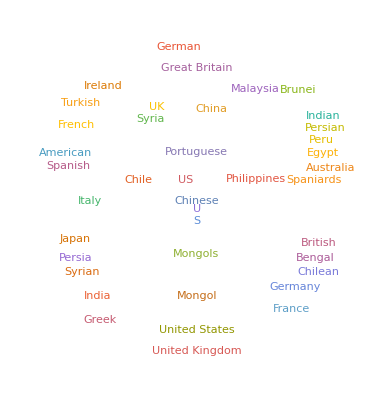

```mathematica
WordCloud@TextCases[WikipediaData["gunpowder"], "Country"]
```

Find all nouns in “She sells seashells by the sea shore.” |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TextCases["She sells seashells by the sea shore.","Noun"]
```

{seashells,sea,shore}

Use TextCases to find the number of nouns, verbs and adjectives in the first 1000 characters of the Wikipedia article on computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TextCases[Characters[WikipediaData["computers"]],"Noun"]
```

{{},{},{c},{o},{m},{p},{u},{t},{},{r},{},{},{s},{},{},{},{d},{},{g},{},{t},{},{l},{},{},{l},{},{c},{t},58051,{u},{t},{},{r},{},{},{b},{y},{},{C},{h},{r},{},{s},{},{G},{},{r},{c},{},{},{},{},{},{t},{},{C},{H},{M}}
 |  |  |  |

```mathematica
{Length@TextCases[
   StringJoin@Take[Characters@WikipediaData["computers"], 1000], 
   "Noun"], 
 Length@TextCases[
   StringJoin@Take[Characters@WikipediaData["computers"], 1000], 
   "Verb"], 
 Length@TextCases[
   StringJoin@Take[Characters@WikipediaData["computers"], 1000], 
   "Adjective"]}
```

{52,25,21}

```mathematica
Length[TextCases[StringTake[WikipediaData["Computers"],1000],#]]&/@{"Noun","Verb","Adjective"}
```

{52,25,21}

Find the grammatical structure of the first sentence of the Wikipedia article about computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TextStructure[TextSentences[WikipediaData["computers"],1]]
```

{    A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinerdigital
Adjectiveelectronic
Adjectivemachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition  carry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause  automatically
Adverb
Adverb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computers"]]]]
(*above soln. worked. Same result obtained*)
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinerdigital
Adjectiveelectronic
Adjectivemachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition  carry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause  automatically
Adverb
Adverb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

Find the 10 most common nouns in ExampleData[{"Text","AliceInWonderland"}]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TextCases[ExampleData[{"Text","AliceInWonderLand"}],"Noun"]
```

ExampleData::notent: "AliceInWonderLand" is not a known entity for the collection "Text". Use ExampleData["Text"] for a list of entities.

TextCases::nlpstrfile: String, File, ContentObject or non-empty list of these textual objects expected for the text at position 1.

TextCases[ExampleData[{Text,AliceInWonderLand}],Noun]

```mathematica
ExampleData[{"Text","AliceInWonderLand"}]
ExampleData[{"Text", "AliceInWonderland"}]
```

ExampleData::notent: "AliceInWonderLand" is not a known entity for the collection "Text". Use ExampleData["Text"] for a list of entities.

ExampleData[{Text,AliceInWonderLand}]

```mathematica
Keys@TakeLargest[Counts[TextCases[ExampleData[{"Text", "AliceInWonderland"}],"Noun"]],10]
```

{door,Rabbit,voice,Mouse,time,way,moment,thing,head,garden}

Make a community graph plot of the graph representation of the text structure of the first sentence of the Wikipedia article about language. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
CommunityGraphPlot[Rule@@@Partition[TextWords[First[TextSentences[WikipediaData["Language"]]]],2,1]]
```

-Graphics-

```mathematica
CommunityGraphPlot[
 First@TextStructure[First@TextSentences[WikipediaData["Language"]], 
   "ConstituentGraph"]]
```

-Graphics-

Make a list of numbers of nouns, verbs, adjectives and adverbs found by WordList in English. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TextCases[WordList[],#]&/@{"Noun","Verb","Adjective","Adverb"}
```

Cloud::timelimit: This computation has exceeded the time limit for your plan.

$Aborted

```mathematica
Length[WordList[#]] & /@ {"Noun", "Verb", "Adjective", "Adverb"}
```

{24493,6503,11392,3120}

Generate a list of the translations of numbers 2 through 10 into French. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
IntegerName[Range[2,10]]
```

{two,three,four,five,six,seven,eight,nine,ten}

```mathematica
Flatten[WordTranslation[#, "French"]&/@IntegerName[Range[2,10]]]
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

```mathematica
Flatten[Table[WordTranslation[IntegerName[n], "French"], {n, 2, 10}]]
(*previous soln worked. prgrm error*)
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

```mathematica
{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}=={deux,trois,quatre,cinq,six,sept,huit,neuf,dix}
```

True